# Datorövning 2: Visualisering

IX1307 Problemlösning i Matematik, Datorövning 2, v1.4

Notebook mall av Göran Andersson

Notera! Klicka på  nedan för att öppna en cell

## 1. Inledning

Data sammanställs ofta i tabeller, men det kan vara väldigt svårt att tyda data i den formen. Genom att visualisera data i ett diagram, blir det mycket tydligare vad datat representerar. Det blir enklare att jämföra resultat och man kan direkt se samband i diagrammet. Exempelvis om man ritar datapunkter i en graf kan det vara enkelt att se om det finns linjära- eller exponentiella funktioner som kan användas för att modellera datat.

## 2. Lärandemål

Efter datorövningen ska studenten kunna :

- använda datorbaserat matematikverktyg för visualisering.
- läsa matematisk text och sätta sig in i nya, matematiskt beskrivna, tillämpningsområden.

## 3. Diagram

### Hantering av data

Datapunkter hanteras som en lista av datapunkter {x, y}.

```mathematica
uidata={{1.0, 0.8}, {2.5, 1.6}, {4.0, 2.1}, {5.0, 2.7}, {6.5, 3.6}, {8.0, 4.2}}
```

{{1.,0.8},{2.5,1.6},{4.,2.1},{5.,2.7},{6.5,3.6},{8.,4.2}}

För att studera ett element kan man använda Part[] eller operatorn [[]]. För att få tredje datapunkten skriver man:

```mathematica
uidata[[3]]
```

{4.,2.1}

För att få x-värdet för tredje datapunkten skriver man

```mathematica
uidata[[3, 1]]
```

4.

och y-värdet:

```mathematica
uidata[[3, 2]]
```

2.1

Använd Mathematicas hjälp för att ta reda på mer information i “guide/ListManipulation”.

### Visualisering av data

Koldioxidhalten i atmosfären har ökat under hela 1900-talet. Följande data beskriver hur koldioxidhalten har ändrats mellan 1930 och 2015.

```mathematica
co2data={{1930, 297}, {1940, 306}, {1950, 314}, {1960, 319}, {1970, 326}, {1980, 339}, {1990, 354}, {2000, 369}, {2010, 389}, {2015, 400}, {2017, 405}, {2018, 408}};
```

Uppmätt data som representerar en tidsserie eller funktion kan bäst visualiseras med ett punktdiagram. Punktdiagram skapas med kommandot ListPlot.

```mathematica
p1=ListPlot[co2data, AxesLabel->{"År", "koldioxidhalt [ppm]"}]
```

Använd Mathematicas hjälp-funktion för att ta reda på hur man kan rita grafen med ett rutnät och där punkterna är sammanbundna med linjer.

### Kurvanpassning

Med hjälp av funktionen FindFit kan man anpassa en modell till datapunkter. Här ett försök att anpassa en linjär modell till CO_2 datat i förgående exempel.

```mathematica
FindFit::usage
```

FindFit[data,expr,pars,vars] finds numerical values of the parameters pars that make expr give a best fit to data as a function of vars. 
FindFit[data,{expr,cons},pars,vars] finds a best fit subject to the parameter constraints cons.

```mathematica
{a1, b1}={a, b}/.FindFit[co2data, {a (t-1930)+b}, {a, b}, t]
```

{1.17756,288.898}

```mathematica
p2=Plot[a1 (t-1930)+b1, {t, 1930, 2020}]
```

För att visa både data och den anpassade funktionen i samma plot, använder vi kommandot Show[]

```mathematica
Show[p1, p2]
```

### Grafritning

Funktionen Plot används för att rita grafer av funktioner. Om man ska rita grafer för funktioner av två variabler kan man använda Plot3D. Plot finns också i varianter med Logaritmiska axlar: LogPlot, LogLogPlot och LogLinearPlot.

```mathematica
p1=Plot[{Exp[3x], 2x^3}, {x, 0, 2}, PlotRange->{{0, 2}, {0,20}}, AxesLabel->{"x", "f(x), g(x)"}]
```

```mathematica
p2=LogPlot[{Exp[3x], 2x^3}, {x, 0, 2}, PlotRange->{{0, 2}, {0.1,20}}, AxesLabel->{"x", "f(x), g(x)"}]
```

```mathematica
p3=LogLogPlot[{Exp[3x], 2x^3}, {x, 0, 2}, PlotRange->{{0.1, 2}, {0.1,20}}, AxesLabel->{"x", "f(x), g(x)"}]
```

```mathematica
p4=Plot3D[Cos[2x]Sin[3y], {x, 0, Pi}, {y,0, Pi}, AxesLabel->{"x", "y", "z"}]
```

### Diagram och visualisering av information

Stapeldiagram används när data är kategoriserad i olika diskreta grupper. Höjden på stapeldiagrammet anger värdet för just den diskreta gruppen. Det finns inget funktionsvärde på x-axeln, bara en beteckning på den diskreta gruppen. Livslön för olika yrkesgrupper är följande

```mathematica
ll={19.1, 15.8, 15.9, 16.4, 18.3};
llLabel={"högskoleingenjör", "gymnasielärare","sjuksköterska", "gymnasieutbildning", "fysiker"};
```

```mathematica
ChartLabels->Placed[{"aaa","bbb","ccc"},Center,Rotate[#,45Degree]&]
```

```mathematica
BarChart[ll,ChartLabels->Placed[llLabel, Center, Rotate[#, 60 Degree] &], AxesLabel->{{},"Livslön [Mkr]"}]
```

Histogram används när data grupperas inom vissa intervall. Antal datapunkter som hamnar inom ett intervall anger y-värdet för just det intervallet. En tärning kan simuleras med hjälp av:

```mathematica
tSlag:= RandomInteger[{1, 6}];
```

1000 tärningslag med två tärningar

```mathematica
data=Table[tSlag+tSlag, {i, 1, 1000}];
```

Fördelningen kan visas i ett histogram :

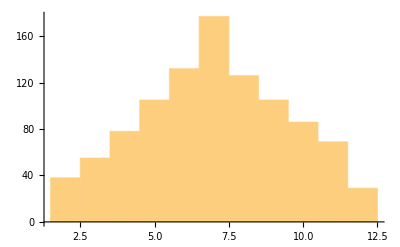

```mathematica
Histogram[data, 11]
```

Fördelningen mellan olika grupper kan anges i ett pajdiagram. Exempelvis är fördelning av fordon i Sverige (tusental fordon)

```mathematica
fdata={4760, 611, 14, 300, 76};
fnamn ={personbil, lastbil, buss, motorcykel, moped};
```

```mathematica
PieChart[fdata, ChartLegends->fnamn, ChartStyle->"DarkRainbow"]
```

-Graphics-

## 4. Trafikflöde

Fordon bör hålla avstånd i trafiken. Rekommendationen är att hålla minst 3 sekunder mellan att fordononet framför passerar en fast punkt och att ens eget fordon passerar samma punkt. Det betyder att högre hastighet ökar trafikflödet men samtidigt så ökar då också avståndet mellan fordon, vilket minskar trafikflödet.

Vi antar att längden på bilarna motsvarar en Volvo v60 = 4,76 m.

```mathematica
l=4.76;
```

Om vi antar att a är avståndet mellan bilarna, v är hastigheten och l är längden på en bil, då är sambandet mellan avstånd till framförvarande bil och hastighet

```mathematica
a=3 v+l
```

Tiden mellan det att två fordon efter varandra passerar en fast punkt är då:

```mathematica
dt=a/v
```

och antal fordon som passerar en punkt per tidsenhet är

```mathematica
q[v_]=1/dt
```

```mathematica
Plot[3600 q[v/3.6],{v, 0, 120}, PlotRange->{{10, 120}, {10, 2000}}, AxesLabel->{"v [km/h]", "flöde [bilar/h]"}]
```

Det vill säga att vid högre hastigheter ökar inte trafikflödet nämnvärt även om medelhastigheten ökar. I realiteten är det dock färre bilar som strikt håller på tre-sekunders regeln för avståndet till framförvarande bil.

## 5. En tredjegradsekvation

En tredjegradsekvation: x^3-x^2-9x+9=0 har tre lösningar. I Mathematica kan man lösa den med kommandot Solve.

```mathematica
f[x_]=x^3-x^2-9x+9
```

```mathematica
Plot[f[x], {x, -5, 5}, AxesLabel->{"x", "f(x)"}]
```

```mathematica
?Solve
```

```mathematica
{x1, x2, x3}=x/.Solve[f[x]==0, x]
```

Ekvationen har lösningarna x_1=-3 ∨ x_2=3 ∨ x_3=1.

```mathematica
Plot[f[x], {x, -5, 5}, AxesLabel->{"x", "f(x)"}, PlotLabel->"Ekvationen x^3-x^2-9x+9=0",Epilog->{PointSize[0.02],Red, Point[{{x1, f[x1]},{x2, f[x2]}, {x3, f[x3]}}]}]
```

## 6. Övningsexempel

### Examensarbete

En student har genomfört ett examensarbete om trafikgenomströmningen på en landsväg, där hen har tagit fram relevant data för examensarbetet. 
Datat består av tre olika mätmängder: antalet fordon av olika fordonstyper som passerar genom landsvägen under en dag, samtliga motorfordons hastighet under 5 min (för kl 8, 12 och 17). Använd introduktionen om Diagram ovan samt exemplet om trafikflöde för att visualisera detta dataset på lämpliga sätt.

Antal fordon: cykel/moped, motorcykel, personbil, lätt lastbil, buss, tung lastbil.

```mathematica
aford={64, 23, 3666,411,11, 63};
```

Hastighet för motorfordon som passerar mätpunkten under 5 min för tidpunkterna kl 8, 12 och 17.

```mathematica
v08={68,71,70,78,92,62,79,71,79,73,87,86,85,85,73,92,100,64,78,85,86,82,72,81,78,73,71,76,92,93,81,94,78,77,82,70,79,63,76,83,82,64,76,71,79,78,71,88,79,72,88,65,81,78,65,71,86,91,81,82,69,90,92,98,79,83,71,52,88,74,68,75,83,91,70,91,84,78,92,83,61,96,75,70,80,91,69,78,79,85,74};
v12={75,64,53,84,94,83,86,70,73,84,88,80,81,65,81,103,59,82,79,67,81,81,72,72,89,96,83,83,68,87,72,56,78,64,82,81,94,81,87,74,83};
v17={97,76,84,57,75,77,78,91,65,78,72,92,73,87,77,67,82,65,75,70,73,85,85,81,83,79,65,80,73,76,69,101,63,71,70,91,95,80,86,77,81,85,75,92,92,77,91,82,83,78,72,77,91,89,62,57,91,73,77,81,66,70,73,75,71,82,87,65,75,73,77,87,83,89,84,69,90,84,80,80,75,102,79,69,71,88,63,65};
```

Visualisera det uppmätta trafikflödet med den teoretiska grafen för trafikflöde om alla motorfordon skulle följa tre-sekunders regeln.

### Ekvationslösning

Hitta lösningarna till polynomekvationen: x^4-3 x^3-12 x^2+6x+20=0 och visualisera resultatet.

### Exponential och Logaritmfunktioner

Rita en graf som visar exponentialfunktionen y=e^(1/3 x) ,  logaritmfunktionen y=3 log_e x och linjen y=x i samma graf. Studera optionen AspectRatio för att justera skalorna på grafen.

### Radioaktiva isotoper

Antag att två radioaktiva ämnen, A och B, har strålningskonstanter 0.02 respektive 0.07. Om en blandning av dessa två ämnen vid tiden t=0 består av M_A gram av ämnet A och M_B gram av ämnet B, kan totala massan y av blandningen beskrivas som

y=M_A e^(-0,02t)+M_B e^(-0,07t)

Antag att M_Aoch M_B är okända men att en forskare har uppmätt total massan vid ett antal tidpunkter (t_i; y_i): 
(10; 21.34), (11;20.6), (12; 20.05), (14; 18.87), (15; 18.30).

a)	Bestäm M_A och M_B med hjälp av funktionen FindFit.
b)	Rita en graf över y(t) där alla mätpunkter finns inprickade.